```mathematica
ClearAll["Global`*"];
pe0=-1;
pn0=0;
(* Subscript[T, 1n] is about 1.5 hours for spin 1 *)
physicalTimes={t1n->1.5*60*60,t1e->0.03};
ω1=1/t1e;
θ=(2c t1e)/t1n;
(*σ=0;*)
(* The complete equations in terms of the polarizations Subscript[P, n], Subscript[P, e], and Subscript[Q, n] *)
peDot=ω1(α(-4/3 pe[t]+pn[t]+1/3 pe[t]qn[t])+β(-4/3 pe[t]-pn[t]+1/3 pe[t]qn[t])-2s pe[t]+σ((2/3 qn[t]-8/3)(pe[t]-pe0)+2pn0 pe[t]pn[t])-2(pe[t]-pe0));
pnDot=ω1 c(α(2/3 pe[t]-1/2 pn[t]-1/6 pe[t]qn[t])+β(-2/3 pe[t]-1/2 pn[t]+1/6 pe[t]qn[t])+θ(-pn[t]-1/3 pn0 qn[t]+4/3 pn0)+σ(-pe0 pe[t]pn[t]-pn[t]-1/3 pn0 qn[t]+4/3 pn0))+ω1 ϕ1(4/3 pn0-1/3 pn0 qn[t]-pn[t])+ω1 ϕ2(4/3 pn0+2/3 pn0 qn[t]-2pn[t]);
qnDot=ω1 c(α(3/2 pe[t]pn[t]-3/2 qn[t])+β(-3/2 pe[t]pn[t]-3/2 qn[t])+θ(3pn0 pn[t]-3qn[t])+σ(3pe0 pe[t]qn[t]+3pn0 pn[t]-3qn[t]))+ϕ1 ω1(3pn0 pn[t]-3qn[t]);
eqns={pe'[t]==peDot,pn'[t]==pnDot,qn'[t]==qnDot,
pe[0]==-1,pn[0]==0,qn[0]==0};
solPhysical=ParametricNDSolve[eqns/.physicalTimes,{pe,pn,qn},{t,0,1*^9},{α,β,s,c,ϕ1,ϕ2,σ}]
Manipulate[Plot[{pe[α,β,s,c,ϕ1,ϕ2,σ][t]/.solPhysical,pn[α,β,s,c,ϕ1,ϕ2,σ][t]/.solPhysical,qn[α,β,s,c,ϕ1,ϕ2,σ][t]/.solPhysical,
(2-Sqrt[4-3(pn[α,β,s,c,ϕ1,ϕ2,σ][t])^2])/.solPhysical},{t,0,2000},
PlotRange->All,ImageSize->Large,PlotLegends->{"P_e","P_n","Q_n","Expected Q_n"}],
{α,0,5},{β,0,5},{s,0,5},{c,0.1*^-4,10*^-4},{ϕ1,0,1*^-4},{ϕ2,0,1*^-4},{σ,0,1}]
```

{pe→ParametricFunction[<>],pn→ParametricFunction[<>],qn→ParametricFunction[<>]}

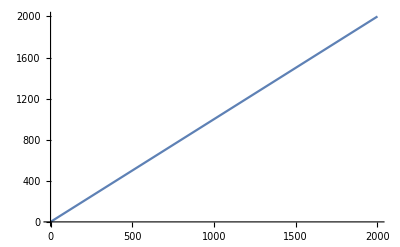

```mathematica
Plot[x,{x,0,2000}]
```